#### import the data

```mathematica
importdata=SemanticImport["D:\\Google Drive\\Rich Internship 2020\\XGBoost\\xgboost_covid\\data\\Data (normalized).csv"];
data1=Values[Normal[importdata]]⟦All,2;;78⟧;
labels=Import["D:\\Google Drive\\Rich Internship 2020\\XGBoost\\xgboost_covid\\data\\Data (normalized).csv"][[1]];
```

## Classification

### Survival probability by age and gender

randomize data for training/test split

```mathematica
SeedRandom[123];
rs=RandomSample[data1⟦All,{1,2,76}⟧,176];
```

Split data into 70% training and 30% test

```mathematica
trainingset=rs⟦1;;123⟧;
testset=rs⟦124;;176⟧;
```

```mathematica
c=Classify[data1⟦All,{1,3,77}⟧->3,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

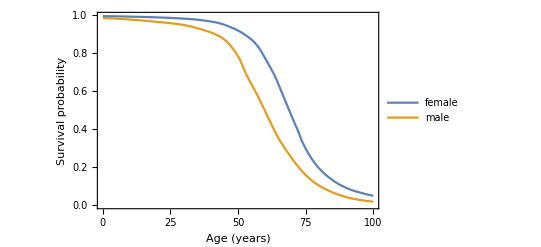

```mathematica
p[age_,gender_]:=c[{age,gender},{"Probability","survived"}];
Plot[{p[x,"female"],p[x,"male"]}, {x,0,100},PlotLegends->{"female","male"}, Frame->True,FrameLabel-> {"Age (years)", "Survival probability"}, Exclusions->None]
```

#### Accuracy and Confusion Matrix

```mathematica
cm=ClassifierMeasurements[c,testset->3]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.792453

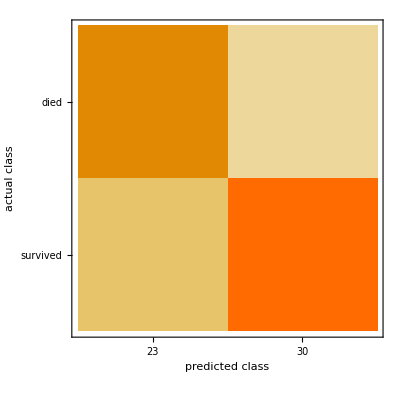

```mathematica
cm["ConfusionMatrixPlot"]
```

## Neural Network approach

#### training/test split of data

randomize data for training/test split

```mathematica
SeedRandom[123];
genrs=Table[RandomSample[data1⟦All,{i,3,77}⟧,176],{i,4,76,1}];
```

Split data into 75% training and 25% test

```mathematica
0.75*176
```

132.

```mathematica
0.25*176
```

44.

```mathematica
trainingset1=Table[genrs⟦i⟧⟦1;;132⟧,{i,1,73}];
testset1=Table[genrs⟦i⟧⟦133;;176⟧,{i,1,73}];
```

### classification by gender

```mathematica
ProgressIndicator[Dynamic[i],{4,76}]
```

```mathematica
c1=Table[Classify[trainingset1⟦i⟧->3,Method->"NeuralNetwork",PerformanceGoal->"Quality"],{i,1,73}];
```

```mathematica
ProgressIndicator[Dynamic[k],{1,73}]
```

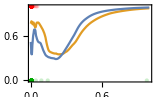
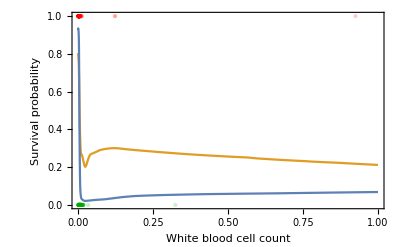
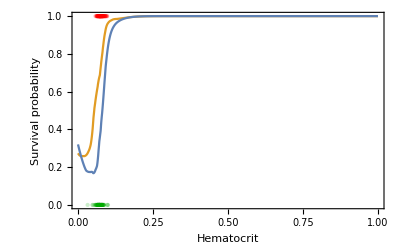
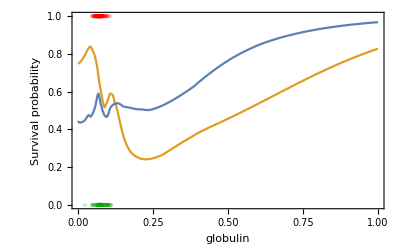
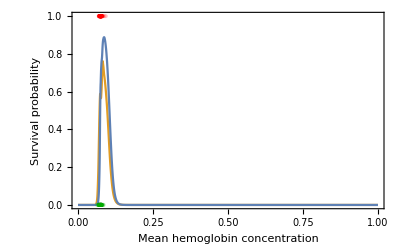
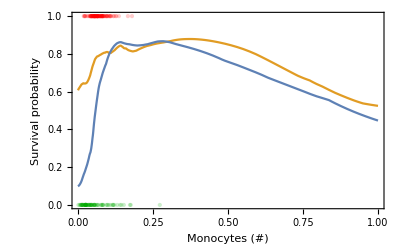
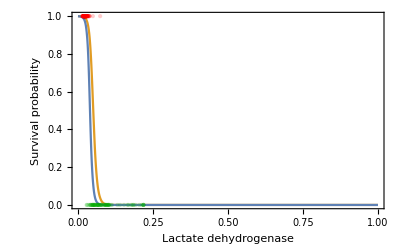
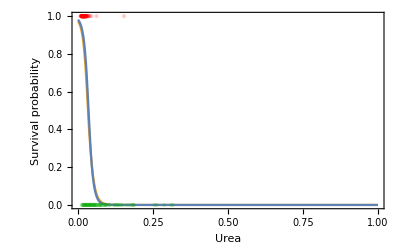
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |  |  |  |

```mathematica
Multicolumn[Table[Show[Plot[{c1⟦k⟧[{x,"female"},{"Probability","survived"}],c1⟦k⟧[{x,"male"},{"Probability","survived"}]}, {x,0,1}, Frame->True,FrameLabel-> {labels⟦4+k⟧, "Survival probability"}, Exclusions->None,PlotRange->{0,1},PlotStyle->{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798]}],ListPlot[{ArrayReshape[Riffle[data1⟦1;;99,3+k⟧,ConstantArray[1,Length[data1⟦1;;99,3+k⟧]]],{Length[data1⟦1;;99,3+k⟧],2}],ArrayReshape[Riffle[data1⟦100;;176,3+k⟧,ConstantArray[0,Length[data1⟦100;;176,3+k⟧]]],{Length[data1⟦100;;176,3+k⟧],2}]},PlotStyle->{Directive[Red,PointSize[Large],Opacity[0.2]],Directive[Darker[Green],PointSize[Large],Opacity[0.2]]}]],{k,1,73,1}],7,Appearance->"Horizontal"]
SwatchLegend[{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]},{"female","male","survived","died"},LegendFunction->"Frame"]
```

```mathematica
Clear[i]
```

```mathematica
Table[cm1⟦i⟧["Accuracy"],{i,1,73,1}]
```

{0.681818,0.727273,0.704545,0.568182,0.568182,0.681818,0.909091,0.840909,0.75,0.5,0.772727,0.795455,0.818182,0.795455,0.75,0.818182,0.75,0.613636,0.727273,0.863636,0.795455,0.75,0.863636,0.613636,0.727273,0.659091,0.727273,0.681818,0.772727,0.454545,0.613636,0.840909,0.704545,0.772727,0.522727,0.727273,0.863636,0.704545,0.727273,0.795455,0.659091,0.818182,0.818182,0.795455,0.818182,0.795455,0.795455,0.590909,0.795455,0.704545,0.636364,0.909091,0.909091,0.659091,0.568182,0.431818,0.590909,0.795455,0.590909,0.659091,0.568182,0.568182,0.75,0.704545,0.75,0.613636,0.795455,0.477273,0.772727,0.818182,0.795455,0.613636,0.795455}

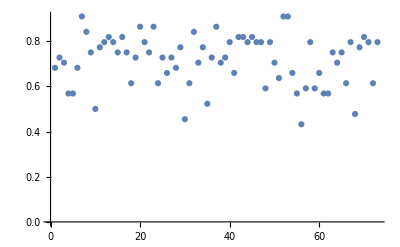

```mathematica
ListPlot[Table[cm1⟦i⟧["Accuracy"],{i,1,73,1}]]
```

#### Confusion matrix and accuracy

```mathematica
cm1=Table[ClassifierMeasurements[c1⟦i⟧,testset⟦i⟧->3],{i,1,73}];
```

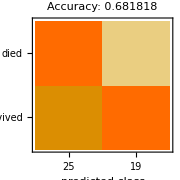
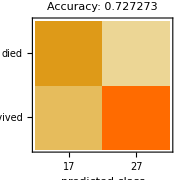
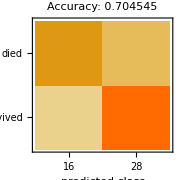
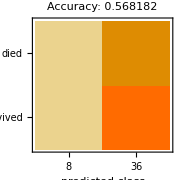
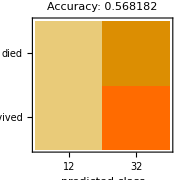
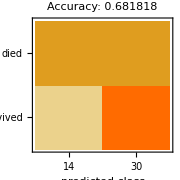
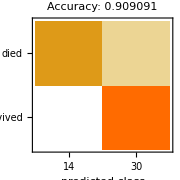
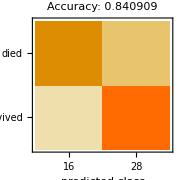
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |  |  |  |

```mathematica
Multicolumn[Table[Show[cm1⟦i⟧["ConfusionMatrixPlot"],ImageSize->Small,PlotLabel->StringJoin["Accuracy: " ,ToString[cm1⟦i⟧["Accuracy"]]]],{i,1,73}],7,Appearance->"Horizontal"]
```

### classification by age group

```mathematica
ProgressIndicator[Dynamic[i],{4,76}]
```

```mathematica
ProgressIndicator[Dynamic[k],{1,73}]
```

```mathematica
c2=Table[Classify[data1⟦All,{i,2,77}⟧->3,Method->"NeuralNetwork",PerformanceGoal->"Quality"],{i,4,76}];
```

```mathematica
Multicolumn[Table[Show[{Plot[{c2⟦k⟧[{x,"young"},{"Probability","survived"}],c2⟦k⟧[{x,"middle age"},{"Probability","survived"}],c2⟦k⟧[{x,"old"},{"Probability","survived"}]}, {x,0,1}, Frame->True,FrameLabel-> {labels⟦4+k⟧, "Survival probability"}, Exclusions->None,PlotRange->{0,1},PlotStyle->{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.915, 0.3325, 0.2125]}],ListPlot[{ArrayReshape[Riffle[data1⟦1;;99,3+k⟧,ConstantArray[1,Length[data1⟦1;;99,3+k⟧]]],{Length[data1⟦1;;99,3+k⟧],2}],ArrayReshape[Riffle[data1⟦100;;176,3+k⟧,ConstantArray[0,Length[data1⟦100;;176,3+k⟧]]],{Length[data1⟦100;;176,3+k⟧],2}]},PlotStyle->{Directive[Red,PointSize[Large],Opacity[0.2]],Directive[Darker[Green],PointSize[Large],Opacity[0.2]]}]}],{k,1,73,1}],7,Appearance->"Horizontal"]
SwatchLegend[{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.915, 0.3325, 0.2125]},{"young","middle age","old"}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |  |  |  |

#### Confusion matrix and accuracy

```mathematica
cm2=Table[ClassifierMeasurements[c2⟦i⟧,testset⟦i⟧->3],{i,1,73}];
```

```mathematica
Multicolumn[Table[Show[cm2⟦i⟧["ConfusionMatrixPlot"],ImageSize->Small,PlotLabel->StringJoin["Accuracy: " ,ToString[cm1⟦i⟧["Accuracy"]]]],{i,1,73}],7,Appearance->"Horizontal"]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |  |  |  |

### Decision Tree Classifier

```mathematica
c3=Classify[data1⟦All,{2,3,77}⟧->3,Method->"NeuralNetwork",PerformanceGoal->"Quality"];
```

```mathematica
Show[TreePlot[{Labeled[1->2,c3[{"young",Missing[]},{"Probability","survived"}]],Labeled[1->3,c3[{"middle age",Missing[]},{"Probability","survived"}]],Labeled[1->4,c3[{"old",Missing[]},{"Probability","survived"}]],Labeled[2->5,c3[{"young","male"},{"Probability","survived"}]],Labeled[2->6,c3[{"young","female"},{"Probability","survived"}]],Labeled[3->7,c3[{"middle age","male"},{"Probability","survived"}]],Labeled[3->8,c3[{"middle age","female"},{"Probability","survived"}]],Labeled[4->9,c3[{"old","male"},{"Probability","survived"}]],Labeled[4->10,c3[{"old","female"},{"Probability","survived"}]]},PlotTheme->"Minimal",VertexLabels->{2->"young",3->"middle age",4->"old",5->"male",6->"female",7->"male",8->"female",9->"male",10->"female"},DirectedEdges->True],ImageSize->Large]
```

-Graphics-

## Clustering analysis

Clustering of lactate dehydrogenase and Hypersensitive c reactive protein.

```mathematica
data2=data1⟦All,{9,42}⟧;
plots=Table[ListPlot[FindClusters[data2,n, Method->"KMeans"],AspectRatio->1,Frame->True,Axes->False,FrameTicks->None],{n,2}];
GraphicsGrid[Partition[plots,2]]
```

-Graphics-

Need to drop Quantification of hepatitis B surface antigen because the ratio just shows Hypersensitive C reactive protein which is the most important feature

```mathematica
ListPlot[{data1⟦All,42⟧,data1⟦All,63⟧},PlotLegends->{"hypersensitive c-reactive protein","Quantification of hepatitis B surface antigen"},PlotRange->All]
```

-Graphics-

```mathematica
c=Classify[data1⟦All,{9,42,76}⟧->3,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

Survival probability of lactate dehydrogenase and Hypersensitive c reactive protein.

```mathematica
p[hsCRP_,LD_]:=c[{hsCRP,LD},{"Probability","survived"}];
Plot3D[{p[x,y]}, {x,-5,10},{y,-5,10},Boxed->True,AxesLabel-> {"Hypersensitive C-reactive protein", "Lactate dehydrogenase","Survival probability"}, Exclusions->None,PlotStyle->Opacity[0.6]]
```

-Graphics3D-

#### Analysis of top 3 features (hs CRP, LD, glucose)

```mathematica
data2=data1⟦All,{9,42,47}⟧;
plots=Table[ListPointPlot3D[FindClusters[data2,n, Method->"KMeans"],AspectRatio->1,Axes->True,AxesLabel->{"hs CRP","LD","glucose"}],{n,2}];
GraphicsGrid[Partition[plots,2]]
```

-Graphics-

```mathematica
Show[%460,ImageSize->Full]
```

-Graphics-

```mathematica
ListPointPlot3D[{data1⟦Range[99],{9,42,47}⟧,data1⟦Range[99]+77,{9,42,47}⟧},PlotStyle->{Blue,Red},PlotLegends->{"patients that survived","patients that died"},AxesLabel->{"lactate dehydrogenase","hypersensitive c-reactive protein","glucose"}]
```

-Graphics3D-